WOLFRAM TECHNOLOGY CONFERENCE  /  JITML

# Just-in-Time Machine Learning

## An adaptive architecture of specialists and generators

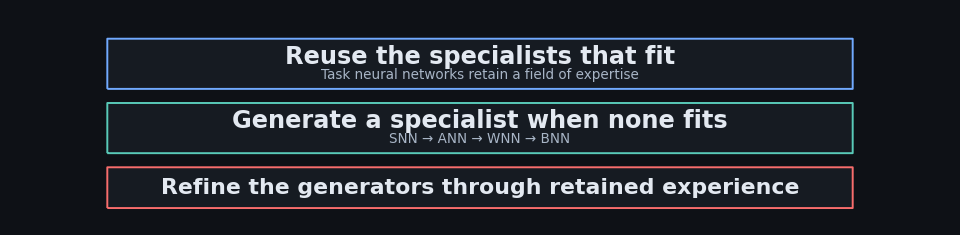

Ghetea Patrick

Copyright (c) 2026 Ghetea Patrick. All rights reserved.

JITML  /  02

## Adapt where the context changes

JITML keeps a changing pool of task specialists. Familiar contexts reuse existing networks; unfamiliar contexts trigger the generation of a new one.

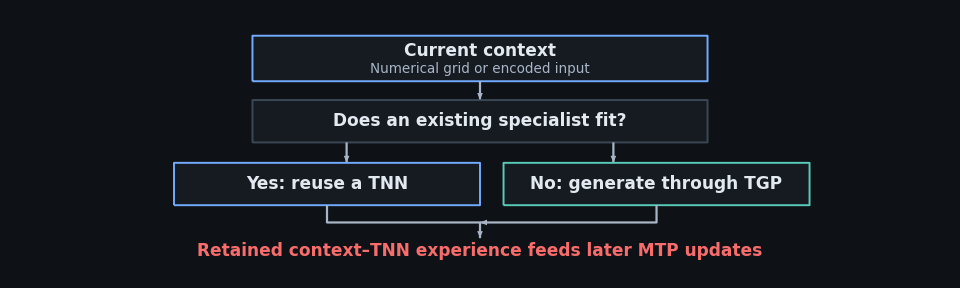

The feedback loop also reaches the generators: meta-training learns from the retained contexts and the TNN definitions associated with them.

JITML  /  03

## Specialists and meta-networks

A TNN performs the immediate task. The MNN suite builds TNNs by separating structure, activations, weights, and biases into four decisions.

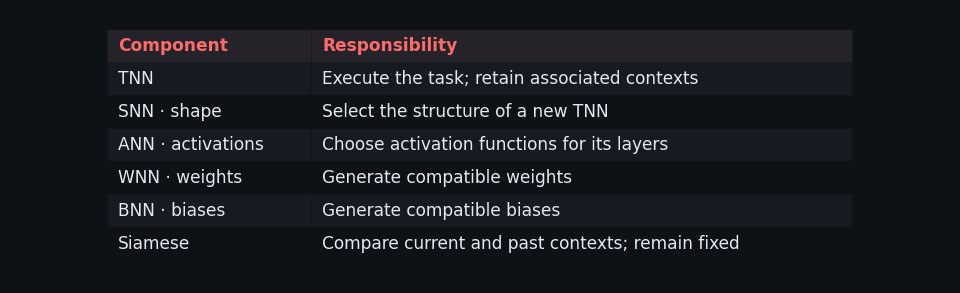

In this architecture, ANN means activation neural network; SNN means shape neural network.

JITML  /  04

## The runtime loop

Ctx holds the environment, the specialist queues, the four MNNs, the fixed matcher, and the scheduling fields. jitml delegates each pass to Step in the order below.

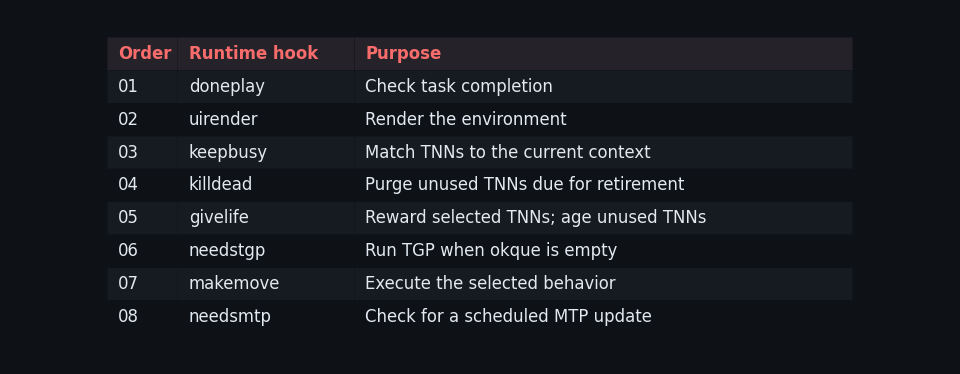

myque: current TNN pool  ·  okque: current matches  ·  dfque: baseline specialists

JITML  /  05

## TGP: build a network definition

The canonical path generates structure, activations, weights, and biases in sequence. Each downstream result must fit the choices made before it.

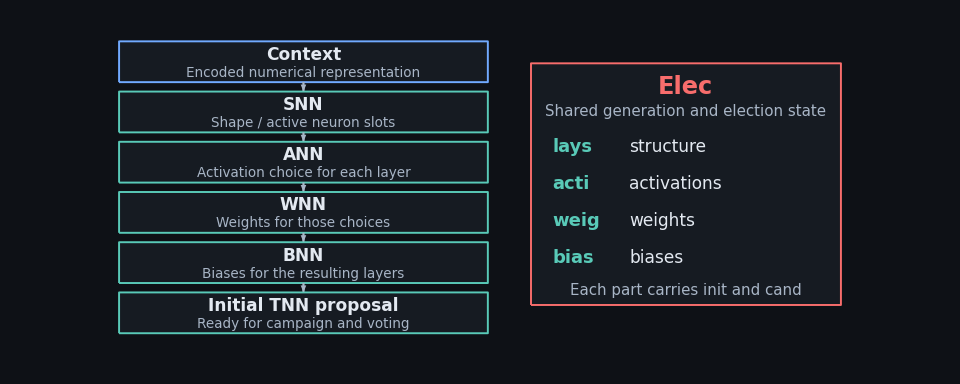

Fixed design choices can bypass their generators; the canonical architecture includes BNN.

JITML  /  06

## Discrete choices on fixed canvases

SNN occupancy outputs decode into layer sizes. ANN outputs select allowed activation functions. The two descriptions form the structural input to parameter generation.

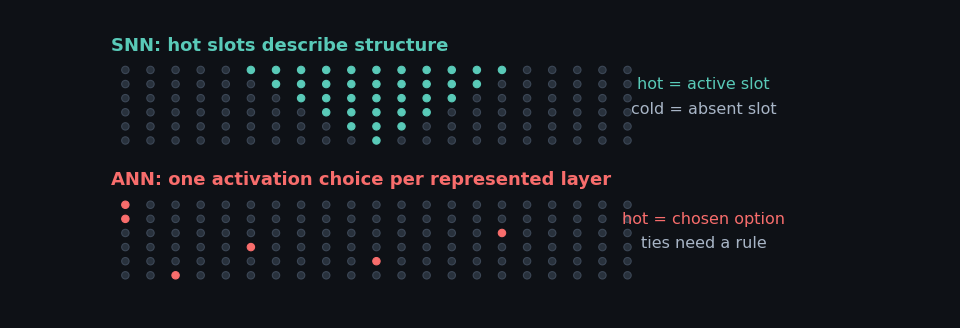

Illustrative intermediate masks from the supplied architecture; they are not preset toy-network dimensions.

JITML  /  07

## Campaign: explore compatible alternatives

For every parameter family, retain the pure proposal and add of_TGP variants. With tnnum = 7, each family has eight entries.

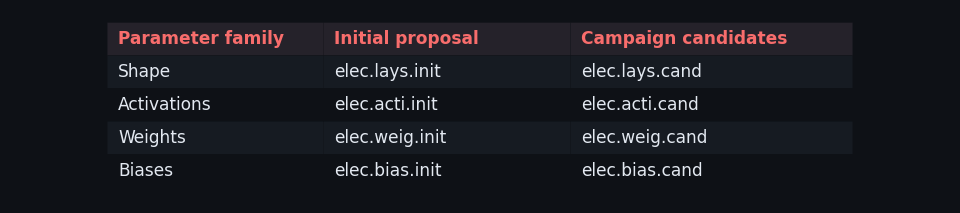

Variants may perturb weights or biases, exchange allowed activations, or change structure. A structural change requires regenerated or patched weights and biases; all dependent choices must still fit.

Candidate counts are per parameter family. The accepted result is one compatible TNN definition.

JITML  /  08

## Voting → Oops when needed → In Office

Criteria may combine deterministic checks, known examples, task feedback, probabilistic scoring, and learned evaluators. Entropy can contribute alongside evidence that the behavior serves the task.

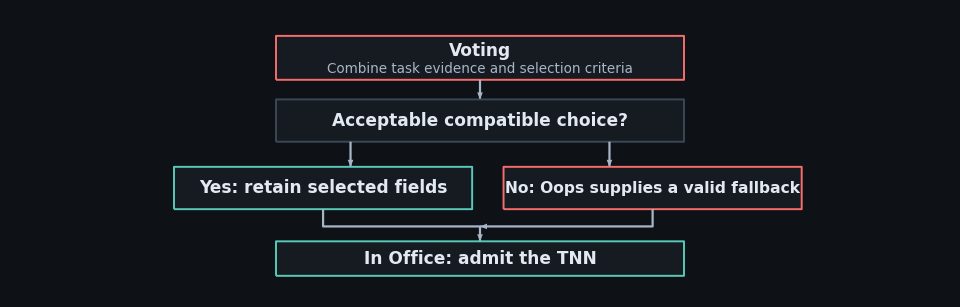

Vote selects fields through the shared Elec object. Oops must ensure a valid fallback when normal criteria reject the proposals; structural validity and task performance remain distinct criteria.

Inference computed during the election can be reused for the selected TNN.

JITML  /  09

## Route by field of expertise

Compare the current context with stored contexts belonging to each TNN. A related context makes that specialist eligible; an empty okque triggers TGP.

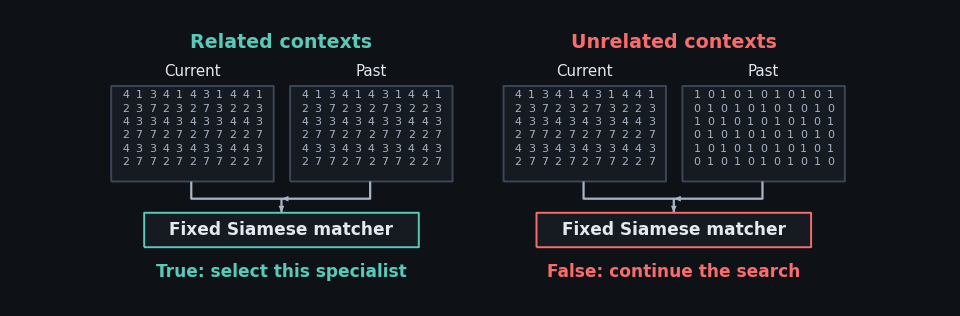

The Boolean examples illustrate the matching contract. The Siamese network remains fixed during TGP and MTP; another matcher may implement the same role.

JITML  /  10

## Usage controls specialist lifetime

The TNN lifespan policy rewards recurring use and ages inactivity. Selected specialists become “hotter”; unused ones become “colder” until retirement.

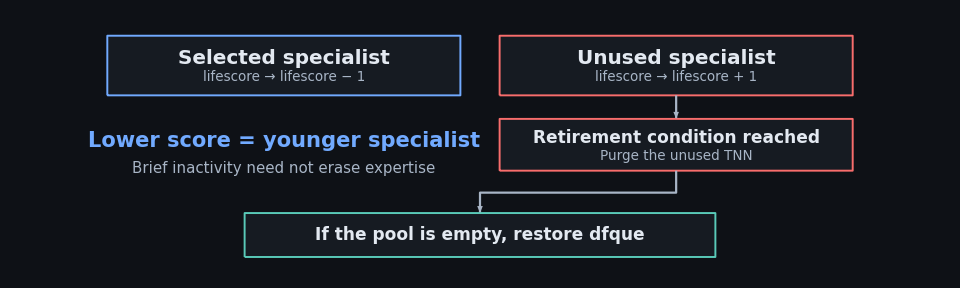

The default TNN set supplies a baseline when the pool is exhausted. An explicit capacity limit is an optional extension; the supplied architecture does not set a hard cap.

JITML  /  11

## Task use and generator use age differently

Reusing a TNN does not by itself age the MNN suite. Generator age tracks actual TGP work, while the MTP clock limits how often the system considers an update.

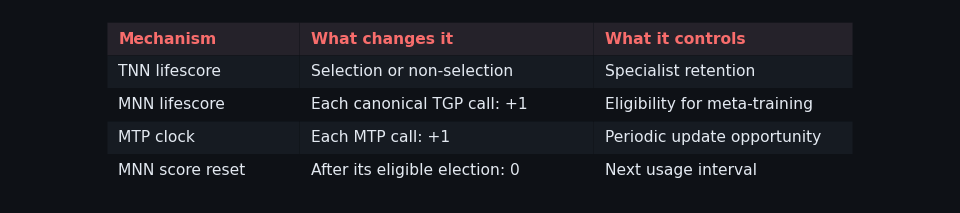

In the canonical TGP, SNN, ANN, WNN, and BNN each gain one lifespan unit. At an eligible MTP election, only the installed winner for that component has its score reset.

JITML  /  12

## MTP: periodic and usage-gated

Every third MTP call opens the clock gate with the current every = 3 setting. Then each MNN is eligible independently when lifescore ≥ lifelimit.

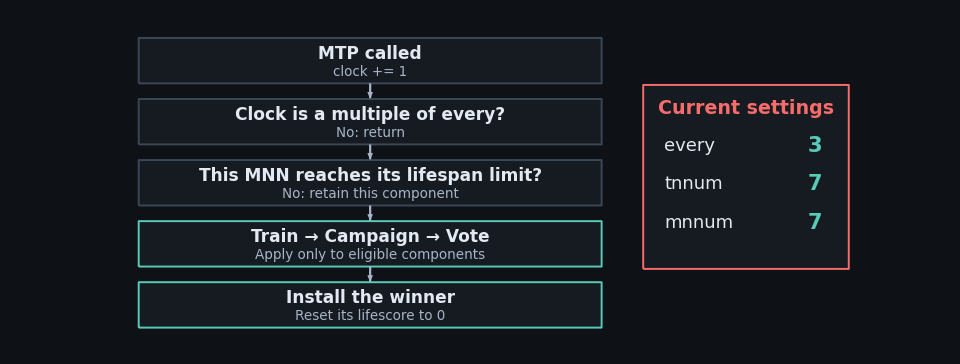

tnnum controls TGP variants per field; mnnum controls MTP variants per eligible MNN election.

JITML  /  13

## Four separate MNN elections

Training is intended to preserve a valid incumbent. Each eligible component competes against alternatives of its own type; the remaining components stay in place.

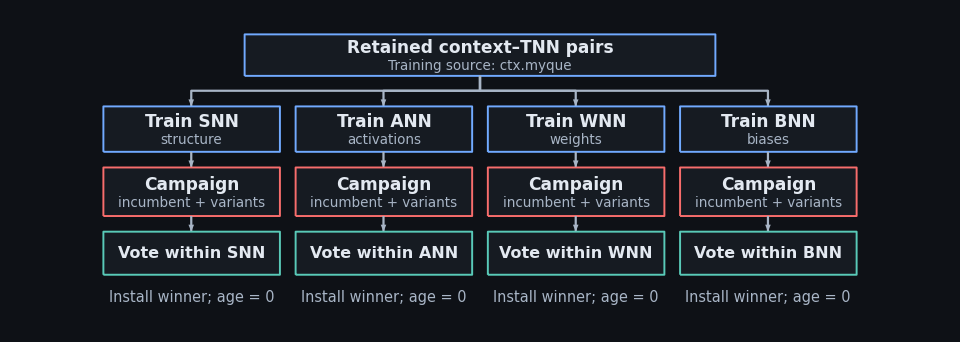

With mnnum = 7, an eligible election includes the incumbent plus seven variants. A valid incumbent remains available, so MTP needs no separate Oops stage.

JITML  /  14

## Toy environment: red and blue tiles

The agent observes a local numerical grid and chooses Up, Dn, Lf, or Rg. Movement is clamped at the edges. The goal condition is reaching the last row.

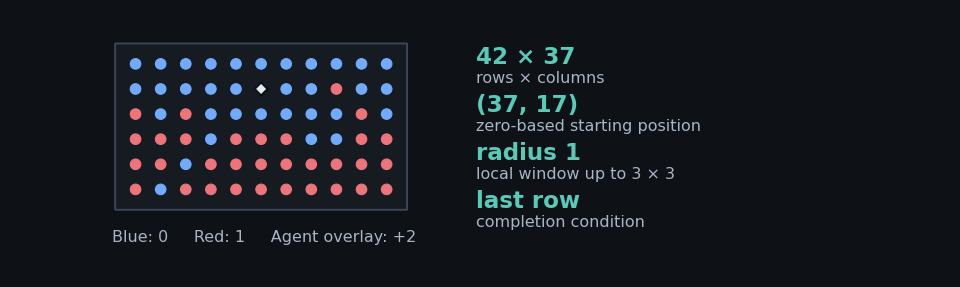

Blue sampling weight decreases down the board. In this version, red weight rises from zero to one and then stays at one. The commands act directly; tile colors supply context.

The compact board is an illustration. The current Env defaults are 42 rows × 37 columns, with Random(42).

JITML  /  15

## Reuse → generate → retain what remains useful

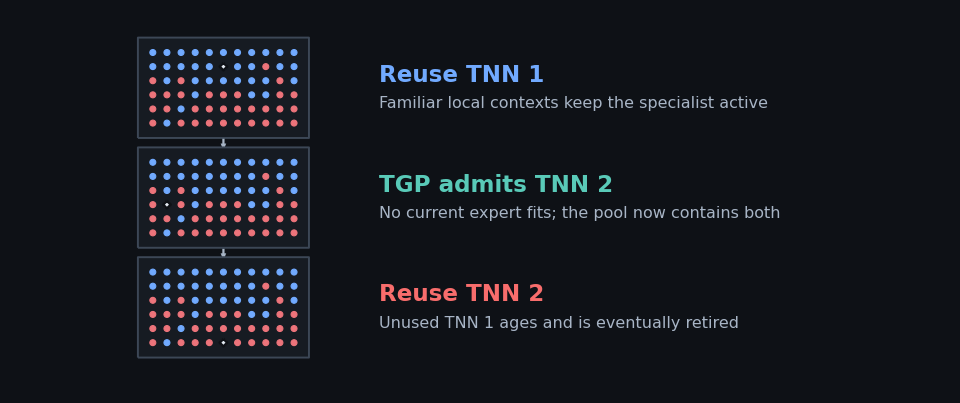

Small changes can still match an existing field of expertise. Generation is needed when routing finds no suitable specialist; continued use then favors the new expert.

Schematic stages from the supplied toy illustration. Each panel may summarize multiple moves; it is not a recorded run.

JITML  /  16

## Flexibility within a shared contract

The full chain describes the general architecture. Simpler deployments can fix some decisions while keeping the same specialist-routing and admission cycle.

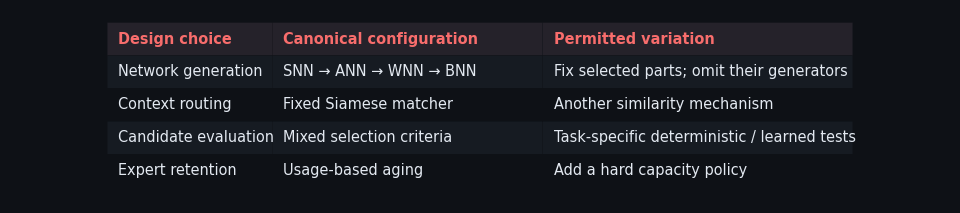

Across these choices, preserve three contracts: a compatible network definition, a valid admission path, and a clear rule for deciding when existing expertise still applies.

JITML  /  17

## Source map

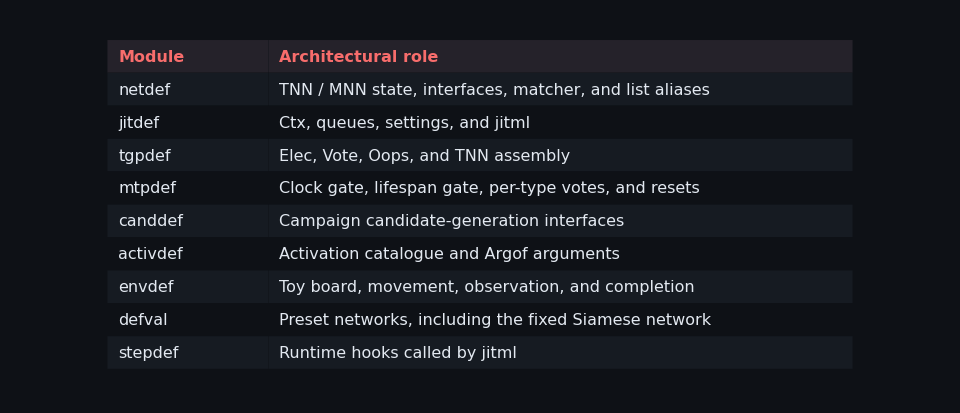

Grid, Cube, and Tess describe two-, three-, and four-level nested-list storage. Layer matrices may differ in size.

JITML  /  18

## Just-in-Time Machine Learning

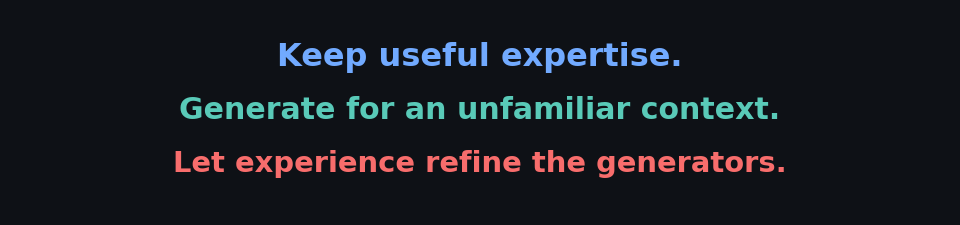

Ghetea Patrick

GitHub: @ghetea-patrick
Email (fast): gheteapatrick@gmail.com
Email (slow): patrick_ghetea@outlook.com

Copyright (c) 2026 Ghetea Patrick. All rights reserved.